## Construct and Parameterize One Enzyme Module

```mathematica
(*Quit[]*)
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TALA";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3_milos_assume_Km_desktop_adjusted_KEQS.csv";

mainFolder = "fit_TALA_FINAL_Format_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

(g3p^c+s7p^c⇌e4p^c+f6p^c)^TALA

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
s7p | Null | 2.42267 | 2.30154
2.54381 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | r5p | 0.031 | 0.02945
0.03255 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 135.599 | 128.819
142.379 | 1/s | 8.5 | 37 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 150.792 | 143.252
158.332 | 1/s | 8.5 | 37 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | f6p | 0.0012 | M | 8.5 | 30 | glygly | 0.05 | 
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | e4p | 0.00009 | M | 8.5 | 30 | glygly | 0.05 | 
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | g3p | 0.000038 | M | 8.5 | 30 | glygly | 0.05 | 
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | s7p | 0.000285 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,0,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities={1,1,1,1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+s7p^c⇌e4p^c+f6p^c)^TALA

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
s7p | Null | 2.42267 | 2.30154
2.54381 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 135.599 | 128.819
142.379 | 1/s | 8.5 | 37 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 150.792 | 143.252
158.332 | 1/s | 8.5 | 37 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | f6p | 0.0012 | M | 8.5 | 30 | glygly | 0.05 | 
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | e4p | 0.00009 | M | 8.5 | 30 | glygly | 0.05 | 
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | g3p | 0.000038 | M | 8.5 | 30 | glygly | 0.05 | 
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | s7p | 0.000285 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_TALA[c] + s7p[c] <=> E_TALA[c]&s7p",
				"E_TALA[c]&s7p <=> E_TALA[c]&MODIFIED&e4p",
				"E_TALA[c]&MODIFIED&e4p <=> E_TALA[c]&MODIFIED + e4p[c]",
				"E_TALA[c]&MODIFIED + g3p[c] <=> E_TALA[c]&MODIFIED&g3p",
				"E_TALA[c]&MODIFIED&g3p <=> E_TALA[c]&f6p",				
				"E_TALA[c]&f6p <=> E_TALA[c] + f6p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TALA^c)_^+s7p^c⇌(TALA^c&s7p^c)_^)^TALA1,((TALA^c&f6p^c)_^⇌(TALA^c)_^+f6p^c)^TALA2,((TALA^c&MODIFIED^c)_^+g3p^c⇌(TALA^c&MODIFIED^c&g3p^c)_^)^TALA3,((TALA^c&s7p^c)_^⇌(TALA^c&MODIFIED^c&e4p^c)_^)^TALA4,((TALA^c&MODIFIED^c&g3p^c)_^⇌(TALA^c&f6p^c)_^)^TALA5,((TALA^c&MODIFIED^c&e4p^c)_^⇌(TALA^c&MODIFIED^c)_^+e4p^c)^TALA6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TALA^c)_^+s7p^c⇌(TALA^c&s7p^c)_^)^TALA1,Overscript[(TALA^c&f6p^c)_^⇌(TALA^c)_^+f6p^c, TALA2],((TALA^c&MODIFIED^c)_^+g3p^c⇌(TALA^c&MODIFIED^c&g3p^c)_^)^TALA3,((TALA^c&s7p^c)_^⇌(TALA^c&MODIFIED^c&e4p^c)_^)^TALA4,((TALA^c&MODIFIED^c&g3p^c)_^⇌(TALA^c&f6p^c)_^)^TALA5,Overscript[(TALA^c&MODIFIED^c&e4p^c)_^⇌(TALA^c&MODIFIED^c)_^+e4p^c, TALA6]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{((TALA^c)_^+pi^c⇌(TALA^c&pi^c)_^)^TALA_Kic_pi_1_f6p,((TALA^c&MODIFIED^c)_^+pi^c⇌(TALA^c&MODIFIED^c&pi^c)_^)^TALA_Kic_pi_1_e4p,((TALA^c&MODIFIED^c)_^+pi^c⇌(TALA^c&MODIFIED^c&pi^c)_^)^TALA_Kic_pi_1_g3p,((TALA^c)_^+pi^c⇌(TALA^c&pi^c)_^)^TALA_Kic_pi_1_s7p}

Generating flux equation...

{((TALA^c&s7p^c)_^-((TALA^c&MODIFIED^c&e4p^c)_^)/K_TALA4) Volume_c k_TALA4^⟶,((TALA^c&MODIFIED^c&g3p^c)_^-((TALA^c&f6p^c)_^)/K_TALA5) Volume_c k_TALA5^⟶}

Volume_c (-(TALA^c&MODIFIED^c&e4p^c)_^ k_TALA4^⟵+(TALA^c&s7p^c)_^ k_TALA4^⟶-(TALA^c&f6p^c)_^ k_TALA5^⟵+(TALA^c&MODIFIED^c&g3p^c)_^ k_TALA5^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
flux = 0.000049390226132;
FluxExpression = absoluteFlux /. {metabolite["s7p", "c"] -> 0.003193, metabolite["g3p", "c"] ->0.000052090795102,metabolite["e4p","c"]-> 0,metabolite["pi","c"]-> 0.0107974519152231,metabolite["f6p","c"]-> 0,
     parameter["TALA_total"] ->0.0000252, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "TALA"] /. FluxExpression;
```

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt"	2.422671439
1	0	0	3.7999999999999996e-6	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.09090909090909091
1	0	0	6.022594131352233e-6	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.13680688860321005
1	0	0	9.545168439736411e-6	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.20076000891310186
1	0	0	0.000015128072481032882	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.2847472489508012
1	0	0	0.00002397637909024733	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0	0.000037999999999999995	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0	0.000060225941313522335	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.6131368201531431
1	0	0	0.00009545168439736412	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0	0.00015128072481032897	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0	0.0002397637909024733	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0	0.00037999999999999997	1	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.9090909090909091
1	9.000000000000007e-6	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.09090909090909098
1	0.000014264038732150038	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.13680688860321014
1	0.000022606977883586257	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.20076000891310197
1	0.00003582964534981475	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.2847472489508014
1	0.00005678616100321741	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.38686317984685703
1	0.00009000000000000007	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.5000000000000002
1	0.00014264038732150037	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.6131368201531432
1	0.00022606977883586258	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.7152527510491988
1	0.00035829645349814786	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.7992399910868985
1	0.0005678616100321741	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.86319311139679
1	0.0009000000000000007	1	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.9090909090909093
1	1	0.00011999999999999995	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.09090909090909088
1	1	0.00019018718309533363	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.13680688860321
1	1	0.0003014263717811494	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.20076000891310164
1	1	0.0004777286046641966	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.28474724895080133
1	1	0.0007571488133762321	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.38686317984685703
1	1	0.0011999999999999995	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.49999999999999994
1	1	0.0019018718309533362	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.613136820153143
1	1	0.0030142637178114944	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.7152527510491984
1	1	0.004777286046641966	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.7992399910868982
1	1	0.007571488133762321	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.8631931113967899
1	1	0.011999999999999995	0	0	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.9090909090909092
1	0	0	1	0.0000285	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.09090909090909093
1	0	0	1	0.000045169455985141756	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.13680688860321005
1	0	0	1	0.00007158876329802309	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.2007600089131019
1	0	0	1	0.00011346054360774674	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.28474724895080145
1	0	0	1	0.000179822843176855	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.38686317984685686
1	0	0	1	0.000285	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.5
1	0	0	1	0.00045169455985141755	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.6131368201531432
1	0	0	1	0.000715887632980231	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.7152527510491988
1	0	0	1	0.0011346054360774674	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.7992399910868982
1	0	0	1	0.00179822843176855	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.86319311139679
1	0	0	1	0.00285	0	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.9090909090909091
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	135.59891603842877
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt"	150.79207189707626
1	1	0.00011999999999999995	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.06249999999999998
1	1	0.00037947331922020535	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.1741123948954683
1	1	0.0011999999999999995	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.3999999999999999
1	1	0.003794733192202054	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.6782688399674104
1	1	0.011999999999999995	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.8695652173913043
1	1	0.00011999999999999995	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.0476190476190476
1	1	0.00037947331922020535	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.13652705949581428
1	1	0.0011999999999999995	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.33333333333333326
1	1	0.003794733192202054	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.6125741132772069
1	1	0.011999999999999995	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.8333333333333333
1	1	0.00011999999999999995	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.03225806451612902
1	1	0.00037947331922020535	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.09535767393825996
1	1	0.0011999999999999995	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.2499999999999999
1	1	0.003794733192202054	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.513167019494862
1	1	0.011999999999999995	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt"	0.769230769230769
1	9.000000000000007e-6	1	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.06250000000000004
1	0.000028460498941515435	1	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.17411239489546843
1	0.00009000000000000007	1	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.40000000000000013
1	0.00028460498941515434	1	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.6782688399674106
1	0.0009000000000000007	1	0	0	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.8695652173913043
1	9.000000000000007e-6	1	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.04761904761904766
1	0.000028460498941515435	1	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.1365270594958144
1	0.00009000000000000007	1	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.33333333333333354
1	0.00028460498941515434	1	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.612574113277207
1	0.0009000000000000007	1	0	0	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.8333333333333336
1	9.000000000000007e-6	1	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.03225806451612906
1	0.000028460498941515435	1	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.09535767393826003
1	0.00009000000000000007	1	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.25000000000000017
1	0.00028460498941515434	1	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.5131670194948621
1	0.0009000000000000007	1	0	0	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt"	0.7692307692307694
1	0	0	3.7999999999999996e-6	1	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.062499999999999986
1	0	0	0.000012016655108639841	1	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.17411239489546834
1	0	0	0.000037999999999999995	1	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.3999999999999999
1	0	0	0.0001201665510863984	1	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.6782688399674105
1	0	0	0.00037999999999999997	1	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.8695652173913043
1	0	0	3.7999999999999996e-6	1	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.04761904761904761
1	0	0	0.000012016655108639841	1	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.1365270594958143
1	0	0	0.000037999999999999995	1	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.33333333333333326
1	0	0	0.0001201665510863984	1	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.6125741132772068
1	0	0	0.00037999999999999997	1	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.8333333333333334
1	0	0	3.7999999999999996e-6	1	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.032258064516129024
1	0	0	0.000012016655108639841	1	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.09535767393825997
1	0	0	0.000037999999999999995	1	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.24999999999999997
1	0	0	0.0001201665510863984	1	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.5131670194948619
1	0	0	0.00037999999999999997	1	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt"	0.7692307692307692
1	0	0	1	0.0000285	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.06250000000000001
1	0	0	1	0.00009012491331479881	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.17411239489546834
1	0	0	1	0.000285	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.39999999999999997
1	0	0	1	0.0009012491331479881	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.6782688399674105
1	0	0	1	0.00285	0.0095	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.8695652173913043
1	0	0	1	0.0000285	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.04761904761904762
1	0	0	1	0.00009012491331479881	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.13652705949581434
1	0	0	1	0.000285	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.3333333333333333
1	0	0	1	0.0009012491331479881	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.6125741132772069
1	0	0	1	0.00285	0.019	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.8333333333333333
1	0	0	1	0.0000285	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.03225806451612904
1	0	0	1	0.00009012491331479881	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.09535767393825997
1	0	0	1	0.000285	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.25
1	0	0	1	0.0009012491331479881	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.513167019494862
1	0	0	1	0.00285	0.038	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt"	0.7692307692307693
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132
3	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt"	0.000049390226132

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	20
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	20
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateFor_s7p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_e4p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/relRateRev_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TALA_FINAL_Format_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 11.0613538731
best_fit: 12.004047583
best_fit: 11.9162699782
best_fit: 12.3681613906
best_fit: 12.0025058139

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | haldaneRatio_1 | 0.358688 | 0.128657 | 1.36194 | 56.2164 | 2.42267 | 1.06073
1 | relRateFor_g3p | 0.0235847 | 0.000556238 | 0.0050734 | 5.58074 | 0.0909091 | 0.0959825
1 | relRateFor_g3p | 0.0223636 | 0.00050013 | 0.00722927 | 5.28429 | 0.136807 | 0.144036
1 | relRateFor_g3p | 0.0206678 | 0.000427158 | 0.00978503 | 4.87399 | 0.20076 | 0.210545
1 | relRateFor_g3p | 0.0184508 | 0.000340433 | 0.012358 | 4.34 | 0.284747 | 0.297105
1 | relRateFor_g3p | 0.0157705 | 0.000248708 | 0.0143063 | 3.69802 | 0.386863 | 0.401169
1 | relRateFor_g3p | 0.01282 | 0.000164353 | 0.0149796 | 2.99592 | 0.5 | 0.51498
1 | relRateFor_g3p | 0.00988948 | 0.0000978018 | 0.0141221 | 2.30326 | 0.613137 | 0.627259
1 | relRateFor_g3p | 0.00726128 | 0.0000527262 | 0.0120594 | 1.68603 | 0.715253 | 0.727312
1 | relRateFor_g3p | 0.00511153 | 0.0000261277 | 0.00946241 | 1.18393 | 0.79924 | 0.808702
1 | relRateFor_g3p | 0.00348168 | 0.0000121221 | 0.00694791 | 0.804908 | 0.863193 | 0.870141
1 | relRateFor_g3p | 0.00231573 | 5.36259×10^-6 | 0.00486036 | 0.53464 | 0.909091 | 0.913951
1 | relRateRev_e4p | 0.238629 | 0.056944 | 0.038431 | 42.2741 | 0.0909091 | 0.0524781
1 | relRateRev_e4p | 0.229258 | 0.0525591 | 0.0561112 | 41.0149 | 0.136807 | 0.0806957
1 | relRateRev_e4p | 0.215853 | 0.0465924 | 0.0786294 | 39.1659 | 0.20076 | 0.122131
1 | relRateRev_e4p | 0.197595 | 0.039044 | 0.104086 | 36.554 | 0.284747 | 0.180661
1 | relRateRev_e4p | 0.174311 | 0.0303843 | 0.127895 | 33.0595 | 0.386863 | 0.258968
1 | relRateRev_e4p | 0.146967 | 0.0215992 | 0.143546 | 28.7092 | 0.5 | 0.356454
1 | relRateRev_e4p | 0.117784 | 0.013873 | 0.145646 | 23.7542 | 0.613137 | 0.467491
1 | relRateRev_e4p | 0.0896468 | 0.00803655 | 0.1334 | 18.6508 | 0.715253 | 0.581852
1 | relRateRev_e4p | 0.0650555 | 0.00423222 | 0.111187 | 13.9116 | 0.79924 | 0.688053
1 | relRateRev_e4p | 0.0453495 | 0.00205658 | 0.0855891 | 9.91541 | 0.863193 | 0.777604
1 | relRateRev_e4p | 0.0306346 | 0.00093848 | 0.0619168 | 6.81085 | 0.909091 | 0.847174
1 | relRateRev_f6p | 0.445978 | 0.198897 | 0.0583533 | 64.1886 | 0.0909091 | 0.0325558
1 | relRateRev_f6p | 0.431642 | 0.186315 | 0.0861701 | 62.9867 | 0.136807 | 0.0506368
1 | relRateRev_f6p | 0.410843 | 0.168792 | 0.122807 | 61.1709 | 0.20076 | 0.0779533
1 | relRateRev_f6p | 0.381921 | 0.145863 | 0.166569 | 58.497 | 0.284747 | 0.118179
1 | relRateRev_f6p | 0.343945 | 0.118299 | 0.211632 | 54.7046 | 0.386863 | 0.175231
1 | relRateRev_f6p | 0.297589 | 0.0885594 | 0.248012 | 49.6023 | 0.5 | 0.251988
1 | relRateRev_f6p | 0.245687 | 0.0603623 | 0.264904 | 43.2047 | 0.613137 | 0.348233
1 | relRateRev_f6p | 0.192838 | 0.0371866 | 0.256455 | 35.8551 | 0.715253 | 0.458798
1 | relRateRev_f6p | 0.143966 | 0.0207263 | 0.225506 | 28.215 | 0.79924 | 0.573734
1 | relRateRev_f6p | 0.102675 | 0.0105423 | 0.181746 | 21.055 | 0.863193 | 0.681448
1 | relRateRev_f6p | 0.0704187 | 0.00495879 | 0.136075 | 14.9682 | 0.909091 | 0.773016
1 | relRateFor_s7p | 0.427507 | 0.182762 | 0.152375 | 167.613 | 0.0909091 | 0.243284
1 | relRateFor_s7p | 0.392233 | 0.153846 | 0.200745 | 146.736 | 0.136807 | 0.337552
1 | relRateFor_s7p | 0.347419 | 0.1207 | 0.246022 | 122.546 | 0.20076 | 0.446782
1 | relRateFor_s7p | 0.294819 | 0.0869184 | 0.276661 | 97.1602 | 0.284747 | 0.561408
1 | relRateFor_s7p | 0.238414 | 0.0568412 | 0.282977 | 73.1465 | 0.386863 | 0.66984
1 | relRateFor_s7p | 0.18344 | 0.0336502 | 0.262799 | 52.5597 | 0.5 | 0.762799
1 | relRateFor_s7p | 0.134649 | 0.0181304 | 0.222864 | 36.3482 | 0.613137 | 0.836001
1 | relRateFor_s7p | 0.0948735 | 0.00900099 | 0.174631 | 24.4152 | 0.715253 | 0.889883
1 | relRateFor_s7p | 0.0646864 | 0.00418433 | 0.128366 | 16.061 | 0.79924 | 0.927606
1 | relRateFor_s7p | 0.0430298 | 0.00185156 | 0.0899053 | 10.4154 | 0.863193 | 0.953098
1 | relRateFor_s7p | 0.0281271 | 0.000791134 | 0.0608258 | 6.69083 | 0.909091 | 0.969917
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.334546 | 0.111921 | 72.835 | 53.7136 | 135.599 | 62.7639
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | absRateRev | 0.375282 | 0.140836 | 87.2448 | 57.8577 | 150.792 | 63.5472
1 | relRateRev_f6p | 0.285241 | 0.0813625 | 0.030093 | 48.1488 | 0.0625 | 0.032407
1 | relRateRev_f6p | 0.259502 | 0.0673414 | 0.0783208 | 44.9829 | 0.174112 | 0.0957916
1 | relRateRev_f6p | 0.202219 | 0.0408924 | 0.148903 | 37.2258 | 0.4 | 0.251097
1 | relRateRev_f6p | 0.119362 | 0.0142473 | 0.162993 | 24.0307 | 0.678269 | 0.515276
1 | relRateRev_f6p | 0.0515812 | 0.00266062 | 0.097381 | 11.1988 | 0.869565 | 0.772184
1 | relRateRev_f6p | 0.169122 | 0.0286023 | 0.0153595 | 32.2549 | 0.047619 | 0.0322596
1 | relRateRev_f6p | 0.155742 | 0.0242556 | 0.0411429 | 30.1353 | 0.136527 | 0.0953842
1 | relRateRev_f6p | 0.124571 | 0.015518 | 0.0831216 | 24.9365 | 0.333333 | 0.250212
1 | relRateRev_f6p | 0.076112 | 0.00579304 | 0.0984753 | 16.0757 | 0.612574 | 0.514099
1 | relRateRev_f6p | 0.0335649 | 0.0011266 | 0.0619792 | 7.4375 | 0.833333 | 0.771354
1 | relRateRev_f6p | 0.00391234 | 0.0000153064 | 0.000289291 | 0.896804 | 0.0322581 | 0.0319688
1 | relRateRev_f6p | 0.00355626 | 0.000012647 | 0.000777656 | 0.815515 | 0.0953577 | 0.09458
1 | relRateRev_f6p | 0.00268235 | 7.19499×10^-6 | 0.00153933 | 0.61573 | 0.25 | 0.248461
1 | relRateRev_f6p | 0.0011911 | 1.41871×10^-6 | 0.00140548 | 0.273884 | 0.513167 | 0.511762
1 | relRateRev_f6p | 0.000264837 | 7.01384×10^-8 | 0.000469227 | 0.0609995 | 0.769231 | 0.7697
1 | relRateRev_e4p | 0.279272 | 0.0779928 | 0.0296445 | 47.4312 | 0.0625 | 0.0328555
1 | relRateRev_e4p | 0.254021 | 0.0645265 | 0.0771041 | 44.2841 | 0.174112 | 0.0970083
1 | relRateRev_e4p | 0.19793 | 0.0391762 | 0.146411 | 36.6028 | 0.4 | 0.253589
1 | relRateRev_e4p | 0.117094 | 0.0137111 | 0.160295 | 23.633 | 0.678269 | 0.517973
1 | relRateRev_e4p | 0.0512702 | 0.00262864 | 0.0968278 | 11.1352 | 0.869565 | 0.772737
1 | relRateRev_e4p | 0.299106 | 0.0894641 | 0.0237038 | 49.7779 | 0.047619 | 0.0239153
1 | relRateRev_e4p | 0.278432 | 0.0775245 | 0.0646175 | 47.3295 | 0.136527 | 0.0719095
1 | relRateRev_e4p | 0.228836 | 0.0523661 | 0.136526 | 40.9577 | 0.333333 | 0.196808
1 | relRateRev_e4p | 0.147052 | 0.0216243 | 0.175951 | 28.7232 | 0.612574 | 0.436623
1 | relRateRev_e4p | 0.0693533 | 0.00480989 | 0.122995 | 14.7594 | 0.833333 | 0.710339
1 | relRateRev_e4p | 0.318616 | 0.101516 | 0.0167691 | 51.9842 | 0.0322581 | 0.015489
1 | relRateRev_e4p | 0.303632 | 0.0921925 | 0.0479637 | 50.2987 | 0.0953577 | 0.047394
1 | relRateRev_e4p | 0.264564 | 0.069994 | 0.114051 | 45.6204 | 0.25 | 0.135949
1 | relRateRev_e4p | 0.188747 | 0.0356254 | 0.180881 | 35.248 | 0.513167 | 0.332286
1 | relRateRev_e4p | 0.099589 | 0.00991796 | 0.15763 | 20.492 | 0.769231 | 0.6116
1 | relRateFor_g3p | 0.00957655 | 0.0000917102 | 0.00136309 | 2.18095 | 0.0625 | 0.0611369
1 | relRateFor_g3p | 0.00844448 | 0.0000713092 | 0.00335276 | 1.92563 | 0.174112 | 0.17076
1 | relRateFor_g3p | 0.00614427 | 0.0000377521 | 0.00561924 | 1.40481 | 0.4 | 0.394381
1 | relRateFor_g3p | 0.00329381 | 0.0000108492 | 0.00512472 | 0.755559 | 0.678269 | 0.673144
1 | relRateFor_g3p | 0.00132335 | 1.75126×10^-6 | 0.00264565 | 0.304249 | 0.869565 | 0.86692
1 | relRateFor_g3p | 0.0259808 | 0.000675004 | 0.00276518 | 5.80688 | 0.047619 | 0.0448539
1 | relRateFor_g3p | 0.023617 | 0.000557765 | 0.00722612 | 5.29281 | 0.136527 | 0.129301
1 | relRateFor_g3p | 0.0183384 | 0.000336296 | 0.0137822 | 4.13466 | 0.333333 | 0.319551
1 | relRateFor_g3p | 0.0107368 | 0.000115279 | 0.0149586 | 2.44193 | 0.612574 | 0.597615
1 | relRateFor_g3p | 0.00463162 | 0.0000214519 | 0.00884002 | 1.0608 | 0.833333 | 0.824493
1 | relRateFor_g3p | 0.042278 | 0.00178743 | 0.00299227 | 9.27605 | 0.0322581 | 0.0292658
1 | relRateFor_g3p | 0.0396401 | 0.00157134 | 0.00831834 | 8.7233 | 0.0953577 | 0.0870393
1 | relRateFor_g3p | 0.0331065 | 0.00109604 | 0.0183493 | 7.33974 | 0.25 | 0.231651
1 | relRateFor_g3p | 0.0217567 | 0.000473353 | 0.0250746 | 4.88625 | 0.513167 | 0.488092
1 | relRateFor_g3p | 0.010421 | 0.000108597 | 0.0182382 | 2.37096 | 0.769231 | 0.750993
1 | relRateFor_s7p | 0.588645 | 0.346503 | 0.179896 | 287.833 | 0.0625 | 0.242396
1 | relRateFor_s7p | 0.460687 | 0.212233 | 0.328829 | 188.86 | 0.174112 | 0.502941
1 | relRateFor_s7p | 0.279851 | 0.0783167 | 0.361923 | 90.4808 | 0.4 | 0.761923
1 | relRateFor_s7p | 0.127699 | 0.0163071 | 0.231856 | 34.1835 | 0.678269 | 0.910125
1 | relRateFor_s7p | 0.047369 | 0.00224382 | 0.10021 | 11.5242 | 0.869565 | 0.969775
1 | relRateFor_s7p | 0.705161 | 0.497252 | 0.193895 | 407.179 | 0.047619 | 0.241514
1 | relRateFor_s7p | 0.565259 | 0.319518 | 0.365212 | 267.501 | 0.136527 | 0.501739
1 | relRateFor_s7p | 0.358534 | 0.128547 | 0.427716 | 128.315 | 0.333333 | 0.76105
1 | relRateFor_s7p | 0.171754 | 0.0294995 | 0.297157 | 48.5095 | 0.612574 | 0.909731
1 | relRateFor_s7p | 0.0657891 | 0.00432821 | 0.136301 | 16.3561 | 0.833333 | 0.969634
1 | relRateFor_s7p | 0.871154 | 0.75891 | 0.207511 | 643.283 | 0.0322581 | 0.239769
1 | relRateFor_s7p | 0.719051 | 0.517034 | 0.403994 | 423.662 | 0.0953577 | 0.499352
1 | relRateFor_s7p | 0.482478 | 0.232785 | 0.509309 | 203.724 | 0.25 | 0.759309
1 | relRateFor_s7p | 0.248278 | 0.061642 | 0.395777 | 77.1243 | 0.513167 | 0.908944
1 | relRateFor_s7p | 0.100425 | 0.0100851 | 0.200121 | 26.0157 | 0.769231 | 0.969352
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338
3 | customRatio_1 | 0.0774601 | 0.00600006 | 9.64362×10^-6 | 19.5254 | 0.0000493902 | 0.0000590338

### Simulated Data and Best Fit Data Plot

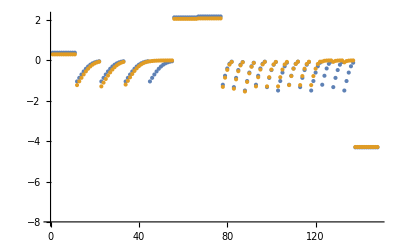

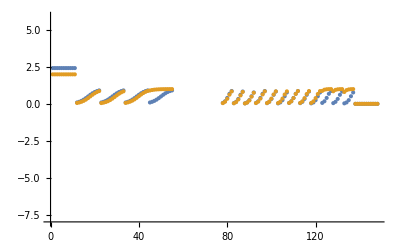

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

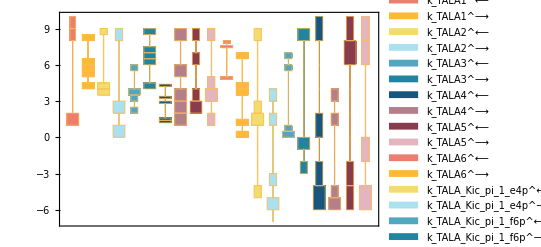

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

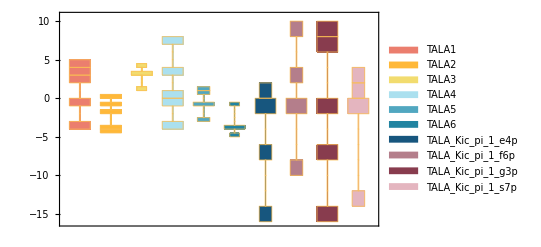

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

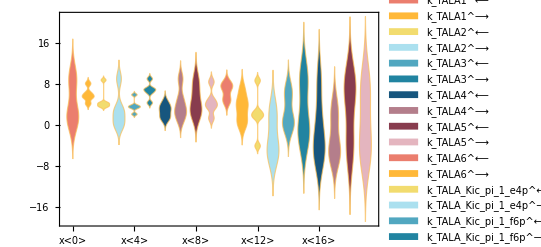

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

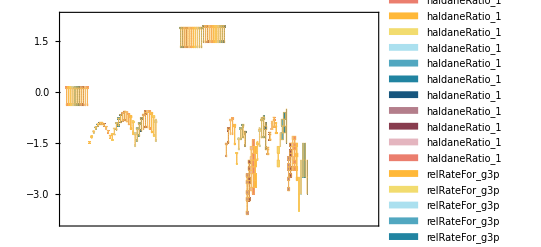

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000038 | 0.0000357894 | 5.81734
0.00009 | 0.000162475 | 80.528
0.0012 | 0.00355373 | 196.144
0.000285 | 0.0000886416 | 68.8977

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
135.599 | 62.7639 | 53.7136
150.792 | 63.5472 | 57.8577

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.42267 | 1.06073 | 56.2164

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.42267 | 1.06073 | 56.2164

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

Part::take: Cannot take positions 1 through 5 in {}.

MapThread::mptd: Object {}⟦1;;5⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$76737,MASSef`Private`x$76737][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

Part::take: Cannot take positions 6 through 10 in {}.

General::stop: Further output of Part::take will be suppressed during this calculation.

MapThread::mptd: Object {}⟦6;;10⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$76737,MASSef`Private`x$76737][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

MapThread::mptd: Object {}⟦11;;15⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$76737,MASSef`Private`x$76737][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

data value | predicted value | error in %
0.019 | Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$76737,MASSef`Private`x$76737],1,1][0]] | 5263.16 Abs[0.019-Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$76737,MASSef`Private`x$76737],1,1][0]]]
0.019 | Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$76737,MASSef`Private`x$76737],1,1][0]] | 5263.16 Abs[0.019-Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$76737,MASSef`Private`x$76737],1,1][0]]]
0.019 | Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$76737,MASSef`Private`x$76737],1,1][0]] | 5263.16 Abs[0.019-Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$76737,MASSef`Private`x$76737],1,1][0]]]
0.019 | Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$76737,MASSef`Private`x$76737],1,1][0]] | 5263.16 Abs[0.019-Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$76737,MASSef`Private`x$76737],1,1][0]]]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 5 in {}.

MapThread::mptd: Object {}⟦1;;5⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$19640,MASSef`Private`x$19640][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

Part::take: Cannot take positions 6 through 10 in {}.

General::stop: Further output of Part::take will be suppressed during this calculation.

MapThread::mptd: Object {}⟦6;;10⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$19640,MASSef`Private`x$19640][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

MapThread::mptd: Object {}⟦11;;15⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$19640,MASSef`Private`x$19640][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{Missing[]},{All,All,All}}]; dimensions are 1 and 3.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{Missing[]},{All,All,All}}]; dimensions are 1 and 3.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{Missing[]},{All,All,All}}]; dimensions are 1 and 3.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

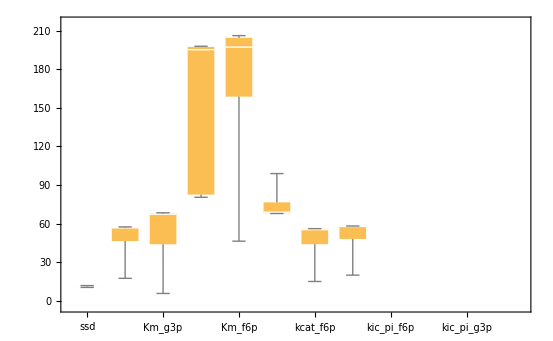

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

```mathematica
{eqnNameList,eqnValList,eqnValListPy,fileList,fileListSub}=exportRateEqs[inputPath,absoluteRateForward,absoluteRateReverse,relativeRateForward,relativeRateReverse,metsSub,metSatForSub,metSatRevSub,rateConstsSub,otherAbsoluteRatesForward,otherAbsoluteRatesReverse];
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 4;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/tala already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/tala\rateconst_labels_tala.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/tala\S_tala.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_TALA[c],E_TALA[c]&f6p,E_TALA[c]&MODIFIED,E_TALA[c]&s7p,E_TALA[c]&MODIFIED&e4p,e4p[c],f6p[c],g3p[c],s7p[c],E_TALA[c]&MODIFIED&g3p,pi[c],E_TALA[c]&pi,E_TALA[c]&MODIFIED&pi}

/Users/guest/Desktop/internship stuff/MASSef/examples/tala\species_tala.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{TALA1: E_TALA[c] + s7p[c] <=> E_TALA[c]&s7p,TALA2: E_TALA[c]&f6p <=> E_TALA[c] + f6p[c],TALA3: E_TALA[c]&MODIFIED + g3p[c] <=> E_TALA[c]&MODIFIED&g3p,TALA4: E_TALA[c]&s7p <=> E_TALA[c]&MODIFIED&e4p,TALA5: E_TALA[c]&MODIFIED&g3p <=> E_TALA[c]&f6p,TALA6: E_TALA[c]&MODIFIED&e4p <=> e4p[c] + E_TALA[c]&MODIFIED,TALA_Kic_pi_1_f6p: E_TALA[c] + pi[c] <=> E_TALA[c]&pi,TALA_Kic_pi_1_e4p: E_TALA[c]&MODIFIED + pi[c] <=> E_TALA[c]&MODIFIED&pi,TALA_Kic_pi_1_g3p: E_TALA[c]&MODIFIED + pi[c] <=> E_TALA[c]&MODIFIED&pi,TALA_Kic_pi_1_s7p: E_TALA[c] + pi[c] <=> E_TALA[c]&pi}

/Users/guest/Desktop/internship stuff/MASSef/examples/tala\reactions_tala.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_TALA[c],E_TALA[c]&f6p,E_TALA[c]&MODIFIED,E_TALA[c]&pi,E_TALA[c]&s7p,E_TALA[c]&MODIFIED&e4p,E_TALA[c]&MODIFIED&g3p,E_TALA[c]&MODIFIED&pi}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

(e4p(c)*k_TALA2_fwd*k_TALA4_rev*k_TALA5_fwd*k_TALA6_rev*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_TALA_total*param_Volume_c**6*(g3p(c)*k_TALA2_fwd*k_TALA3_fwd*(k_TALA1_rev + k_TALA4_fwd)*k_TALA5_fwd*(k_TALA4_rev + k_TALA6_fwd)*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**6 + k_TALA4_rev*param_Volume_c*(-(g3p(c)*k_TALA2_fwd*k_TALA3_fwd*k_TALA4_fwd*k_TALA5_fwd*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**5) - e4p(c)*k_TALA1_rev*k_TALA6_rev*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**3*(k_TALA5_fwd*k_TALA5_rev*param_Volume_c**2 - (k_TALA3_rev + k_TALA5_fwd)*(k_TALA2_fwd + k_TALA5_rev)*param_Volume_c**2))))/(-((k_TALA4_rev*param_Volume_c*(e4p(c)*k_TALA6_rev*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**2*(k_TALA2_fwd*k_TALA5_fwd*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**3 - k_TALA1_rev*param_Volume_c*(k_TALA5_fwd*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**2 + (k_TALA2_fwd + k_TALA5_rev)*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**2)) - k_TALA2_fwd*k_TALA4_fwd*k_TALA5_fwd*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**4*((k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c + (k_TALA_Kic_pi_1_e4p_fwd + k_TALA_Kic_pi_1_g3p_fwd)*param_Volume_c*pi(c))) + (k_TALA1_rev + k_TALA4_fwd)*param_Volume_c*(e4p(c)*k_TALA2_fwd*k_TALA5_fwd*k_TALA6_rev*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**5 + k_TALA2_fwd*k_TALA5_fwd*(k_TALA4_rev + k_TALA6_fwd)*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**4*((k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c + (k_TALA_Kic_pi_1_e4p_fwd + k_TALA_Kic_pi_1_g3p_fwd)*param_Volume_c*pi(c))))*(-(g3p(c)*k_TALA1_fwd*k_TALA2_fwd*k_TALA3_fwd*k_TALA5_fwd*(k_TALA4_rev + k_TALA6_fwd)*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**6*s7p(c)) + e4p(c)*k_TALA4_rev*k_TALA6_rev*param_Volume_c**2*(-((k_TALA_Kic_pi_1_f6p_fwd + k_TALA_Kic_pi_1_s7p_fwd)*param_Volume_c*(k_TALA_Kic_pi_1_f6p_rev*param_Volume_c + k_TALA_Kic_pi_1_s7p_rev*param_Volume_c)*(k_TALA5_fwd*k_TALA5_rev*param_Volume_c**2 - (k_TALA3_rev + k_TALA5_fwd)*(k_TALA2_fwd + k_TALA5_rev)*param_Volume_c**2)*pi(c)) + (k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c*(f6p(c)*k_TALA2_fwd*k_TALA2_rev*(k_TALA3_rev + k_TALA5_fwd)*param_Volume_c**3 + param_Volume_c*(k_TALA5_fwd*k_TALA5_rev*param_Volume_c**2 - (k_TALA3_rev + k_TALA5_fwd)*(k_TALA2_fwd + k_TALA5_rev)*param_Volume_c**2)*(f6p(c)*k_TALA2_rev + (k_TALA_Kic_pi_1_f6p_fwd + k_TALA_Kic_pi_1_s7p_fwd)*pi(c) + k_TALA1_fwd*s7p(c)))))) + (g3p(c)*k_TALA2_fwd*k_TALA3_fwd*(k_TALA1_rev + k_TALA4_fwd)*k_TALA5_fwd*(k_TALA4_rev + k_TALA6_fwd)*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**6 + k_TALA4_rev*param_Volume_c*(-(g3p(c)*k_TALA2_fwd*k_TALA3_fwd*k_TALA4_fwd*k_TALA5_fwd*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**5) - e4p(c)*k_TALA1_rev*k_TALA6_rev*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**3*(k_TALA5_fwd*k_TALA5_rev*param_Volume_c**2 - (k_TALA3_rev + k_TALA5_fwd)*(k_TALA2_fwd + k_TALA5_rev)*param_Volume_c**2)))*(-(k_TALA1_fwd*param_Volume_c*(e4p(c)*k_TALA2_fwd*k_TALA5_fwd*k_TALA6_rev*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**5 + k_TALA2_fwd*k_TALA5_fwd*(k_TALA4_rev + k_TALA6_fwd)*(k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c**4*((k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c + (k_TALA_Kic_pi_1_e4p_fwd + k_TALA_Kic_pi_1_g3p_fwd)*param_Volume_c*pi(c)))*s7p(c)) + e4p(c)*k_TALA4_rev*k_TALA6_rev*param_Volume_c**2*((k_TALA_Kic_pi_1_f6p_fwd + k_TALA_Kic_pi_1_s7p_fwd)*param_Volume_c*(k_TALA2_fwd*k_TALA5_fwd*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**3 - (k_TALA_Kic_pi_1_f6p_rev*param_Volume_c + k_TALA_Kic_pi_1_s7p_rev*param_Volume_c)*(k_TALA5_fwd*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**2 + (k_TALA2_fwd + k_TALA5_rev)*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**2))*pi(c) + (k_TALA_Kic_pi_1_f6p_rev + k_TALA_Kic_pi_1_s7p_rev)*param_Volume_c*(k_TALA2_fwd*param_Volume_c*(-(f6p(c)*k_TALA2_rev*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**2) + k_TALA5_fwd*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**2) + param_Volume_c*(k_TALA5_fwd*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**2 + (k_TALA2_fwd + k_TALA5_rev)*(k_TALA_Kic_pi_1_e4p_rev + k_TALA_Kic_pi_1_g3p_rev)*param_Volume_c**2)*(f6p(c)*k_TALA2_rev + (k_TALA_Kic_pi_1_f6p_fwd + k_TALA_Kic_pi_1_s7p_fwd)*pi(c) + k_TALA1_fwd*s7p(c))))))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/tala\rateconst_clusters_tala.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/tala\rateLaw_tala.txt

```mathematica
"/Users/guest/Desktop/internship stuff/MASSef/examples/tala\\rateLaw_tala.txt"
NotebookClose[]
```